# Lorentz Transform Test Cases

See Mihalas & Mihalas, Eq. 89.5-8

## γ

```mathematica
c= 2.99792458 10^10
```

2.99792×10^10

```mathematica
gamma[v_]:=1/Sqrt[1 - v.v/(c * c)]
```

```mathematica
norm[v_]:=Sqrt[v.v]
```

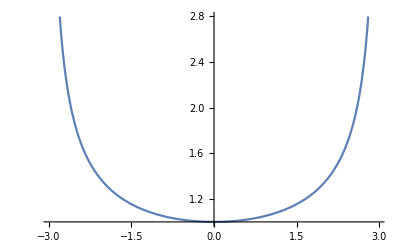

```mathematica
Plot[gamma[{v}],{v,-0.99*c,0.99*c}]
```

### γ Test Cases

```mathematica
makeVel[]:=With [{v = {N[RandomReal[{-0.99 c,0.99 c}],15],N[RandomReal[{-0.99 c,0.99 c}],15],N[RandomReal[{-0.99 c,0.99 c}],15]}},If[norm[v]<c,v,makeVel[]]]
```

```mathematica
cases1=Table[{N[#,15],N[gamma[#],15]}&[makeVel[]],{i,1,10}]
```

{{{9.52804×10^9,-2.26309×10^10,-9.35836×10^9},2.07752},{{2.3648×10^9,-2.33919×10^10,2.36034×10^9},1.62488},{{-8.74903×10^9,3.89354×10^9,-2.93014×10^9},1.06095},{{-2.29945×10^10,-1.60644×10^9,-1.77013×10^10},4.0761},{{-7.86237×10^9,-1.84941×10^10,-4.48379×10^9},1.37583},{{1.13431×10^10,8.9539×10^9,-3.78838×10^9},1.15342},{{1.89381×10^10,-5.08761×10^9,-1.69128×10^10},1.98466},{{1.53228×10^9,2.07845×10^10,9.77271×10^9},1.56085},{{-1.43662×10^10,1.89798×10^10,-5.85537×10^9},1.73709},{{1.1131×10^9,4.8818×10^9,-1.36046×10^9},1.01532}}

## LTs

```mathematica
ltEToCom[elab_, vmatInLab_, dirLab_]:=gamma[vmatInLab]*elab * (1-dirLab.vmatInLab / c)
```

```mathematica
ltEToLab[ecom_, vmatInLab_, dircom_]:=gamma[vmatInLab]*ecom * (1+dircom.vmatInLab / c)
```

```mathematica
ltΩToLab[elab_,ecom_, vmatInLab_, dircom_]:=With[{gv=gamma[vmatInLab]},ecom/elab*(dircom + gv*vmatInLab/c(1+gv*dircom.vmatInLab/c/(gv+1)))]
```

```mathematica
ltΩToCom[ecom_,elab_, vmatInLab_, dirlab_]:=With[{gv=gamma[vmatInLab]},elab/ecom*(dirlab - gv*vmatInLab/c*(1-gv*(dirlab.vmatInLab)/c/(gv+1)))]
```

#### Plots

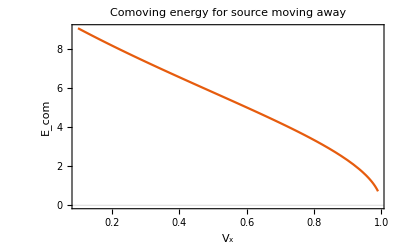

```mathematica
Plot[ltEToCom[10,{v c,0,0},{1,0,0}],{v,0.1,0.99},PlotTheme->"Scientific",PlotLabel->"Comoving energy for source moving away",Frame->True,FrameLabel->{"\!\(\*SubscriptBox[\(V\), \(x\)]\)","\!\(\*SubscriptBox[\(E\), \(com\)]\)"},LabelStyle->{"Helvettica"}]
```

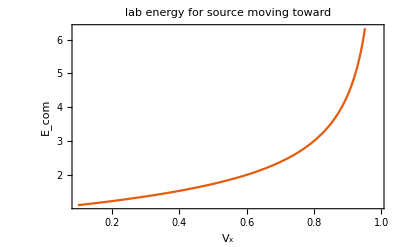

```mathematica
Plot[ltEToLab[1,{v c,0,0},{1,0,0}],{v,0.1,0.99},PlotTheme->"Scientific",PlotLabel->"lab energy for source moving toward",Frame->True,FrameLabel->{"\!\(\*SubscriptBox[\(V\), \(x\)]\)","\!\(\*SubscriptBox[\(E\), \(com\)]\)"},LabelStyle->{"Helvettica"}]
```

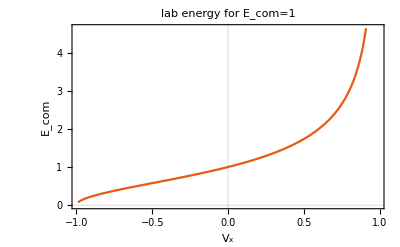

```mathematica
Plot[ltEToLab[1,{v c,0,0},{1,0,0}],{v,-0.99,0.99},PlotTheme->"Scientific",PlotLabel->"lab energy for E_com=1",Frame->True,FrameLabel->{"\!\(\*SubscriptBox[\(V\), \(x\)]\)","\!\(\*SubscriptBox[\(E\), \(com\)]\)"},LabelStyle->{"Helvettica"}]
```

### Test Cases

```mathematica
mkDirection[]:=With[{cosTheta=2*RandomReal[]-1,phi=2*π*RandomReal[]},{N[√(1-cosTheta*cosTheta) Cos[phi],15],N[√(1-cosTheta*cosTheta) Sin[phi],15],N[cosTheta,15]}]
```

#### These are inputs, can be used as either {E_lab,V_lab,Ω_lab} or {E_com,V_com,Ω_com}

```mathematica
tcases=Table[{RandomReal[{0,1000}],makeVel[],mkDirection[]},{i,1,100}]
```

{{385.911,{-1.60121×10^10,6.45014×10^9,9.98383×10^9},{-0.925253,0.36699,-0.0960471}},{501.439,{-2.05524×10^10,-1.2342×10^10,1.47168×10^10},{0.739251,0.631872,0.232908}},{73.315,{-1.07798×10^10,9.986×10^9,-1.84115×10^10},{0.957955,0.0682776,0.278677}},{794.442,{-7.50365×10^9,1.06061×10^10,-1.3899×10^10},{0.503187,-0.278753,-0.817985}},{404.471,{-1.70585×10^10,7.03037×10^9,2.1835×10^10},{-0.214649,0.711251,0.669364}},{960.863,{-5.3651×10^9,1.61102×10^10,-2.58026×10^9},{-0.409502,0.705583,-0.578326}},{188.394,{9.4588×10^8,-1.99868×10^10,2.18873×10^10},{-0.260119,-0.802121,-0.537532}},{985.196,{-1.95697×10^10,2.19742×10^8,-1.58624×10^10},{-0.713176,-0.218608,-0.666026}},{296.13,{-1.14799×10^10,-9.81733×10^9,1.68782×10^10},{-0.164306,-0.397458,-0.902791}},{691.066,{3.22423×10^9,2.54579×10^10,6.84211×10^9},{-0.477365,-0.829385,-0.290247}},{586.564,{-3.56157×10^9,-7.74772×10^9,-1.4094×10^10},{-0.228991,0.921952,-0.312359}},{432.722,{2.02531×10^10,2.30891×10^9,7.37864×10^9},{0.809204,0.58538,0.0501963}},{757.265,{3.62841×10^9,7.61912×10^9,3.43144×10^9},{0.300653,-0.945745,0.123187}},{423.575,{-2.1142×10^10,2.0784×10^7,-2.96693×10^9},{0.981098,-0.192938,-0.0148898}},{713.933,{7.9584×10^9,-1.51583×10^9,-1.41102×10^10},{-0.324241,-0.286309,0.901607}},{824.985,{-4.55258×10^9,-9.74806×10^9,-5.19384×10^9},{-0.824852,-0.0436732,-0.56366}},{31.3914,{1.13186×10^10,-3.37902×10^9,-2.49936×10^10},{0.0602631,-0.647582,0.759609}},{917.512,{9.42409×10^8,4.95292×10^9,8.65271×10^9},{-0.55106,0.0895753,0.829644}},{128.717,{-1.23492×10^10,-1.43335×10^10,7.05637×10^9},{-0.975413,-0.199191,0.0942971}},{22.7027,{-1.00599×10^10,-1.97326×10^10,-9.50465×10^9},{0.697856,0.628631,0.343248}},{163.542,{-5.42677×10^9,-1.80341×10^10,-2.28602×10^10},{-0.281525,-0.775012,-0.565774}},{728.647,{-9.34835×10^9,2.31303×10^10,1.27755×10^10},{0.206606,0.830984,-0.516508}},{835.095,{1.30288×10^10,1.13167×10^10,2.26034×10^10},{0.530847,-0.723503,-0.4413}},{795.393,{1.33833×10^10,-1.60965×10^10,-1.6645×10^8},{0.276915,0.107492,0.954863}},{191.138,{-1.69036×10^10,-2.91409×10^9,-1.70353×10^10},{0.289877,0.714896,0.636314}},{103.996,{1.80639×10^10,-1.07462×10^10,-1.62955×10^10},{0.611606,-0.723281,-0.320627}},{253.537,{-1.79468×10^10,6.17859×10^9,3.96085×10^9},{0.565797,-0.723849,-0.394863}},{338.226,{-1.72004×10^9,2.0705×10^10,-7.22514×10^9},{-0.126202,0.851491,0.508956}},{235.257,{8.11617×10^9,-1.10172×10^10,-7.6206×10^9},{0.263418,-0.396338,-0.879504}},{393.461,{-1.675×10^10,-5.9718×10^9,1.833×10^10},{-0.116034,0.926,-0.359249}},{109.622,{3.5598×10^9,-1.08206×10^10,2.71556×10^10},{0.564085,-0.713969,0.414797}},{378.383,{-4.3356×10^9,5.08317×10^9,2.05458×10^10},{-0.125376,0.827067,0.547942}},{888.729,{-9.34836×10^9,2.67093×10^10,-4.22299×10^8},{0.0912568,0.409675,-0.907656}},{682.585,{1.97257×10^10,-3.92744×10^9,-1.96222×10^10},{0.964,0.0200656,0.265144}},{148.253,{-3.26846×10^9,-2.16716×10^10,-1.92302×10^10},{-0.816117,0.107987,0.567708}},{587.257,{2.48522×10^10,8.9502×10^8,5.67297×10^9},{-0.0956549,-0.994927,0.0311424}},{946.323,{-1.66894×10^10,4.08723×10^8,3.41151×10^9},{-0.485599,-0.53857,0.688575}},{599.016,{-2.55355×10^10,1.5341×10^9,-1.01178×10^10},{0.702121,-0.704118,0.106038}},{288.475,{8.05932×10^9,4.60662×10^9,7.79696×10^9},{0.352987,-0.107887,0.929387}},{296.494,{-1.57806×10^10,2.96767×10^9,1.64441×10^10},{-0.829261,0.362915,-0.424992}},{827.336,{2.34628×10^9,1.50405×10^10,-6.81725×10^9},{0.769495,0.571107,0.285858}},{730.363,{-2.87931×10^10,-2.57037×10^9,2.09667×10^9},{-0.66373,-0.519616,0.538017}},{733.946,{6.27063×10^9,1.21808×10^10,-1.20966×10^10},{0.310178,0.0195598,-0.950477}},{568.094,{-1.49324×10^10,8.41787×10^8,-1.48059×10^10},{-0.828729,-0.330631,-0.451543}},{326.582,{1.30032×10^10,-3.35582×10^8,-2.32096×10^10},{0.75974,-0.183236,0.623874}},{224.704,{-1.49536×10^10,1.94677×10^10,1.5199×10^10},{0.957957,-0.276935,-0.0750055}},{664.551,{-4.77171×10^9,2.89378×10^9,2.25356×10^10},{0.847198,-0.419793,-0.325622}},{208.899,{-6.07437×10^9,-9.71527×10^9,-4.85483×10^9},{0.74461,-0.141394,0.652353}},{626.408,{1.31828×10^10,1.67457×10^10,-9.22819×10^9},{-0.0319072,-0.0767967,-0.996536}},{443.853,{-1.60143×10^10,6.90657×10^9,8.89797×10^9},{0.384807,0.471949,-0.793214}},{737.033,{1.81969×10^10,1.90432×10^10,-9.77515×10^9},{-0.385775,-0.914565,0.121442}},{283.002,{-1.65593×10^10,5.8674×10^9,-2.14228×10^10},{-0.587889,0.761458,-0.273072}},{699.454,{2.4655×10^9,1.50992×10^10,-1.85446×10^10},{0.317153,-0.645994,-0.694338}},{801.866,{6.86483×10^9,-2.25055×10^10,1.50437×10^10},{0.338731,0.194348,-0.920592}},{81.1913,{1.19894×10^10,2.05717×10^9,-4.66739×10^8},{0.310776,-0.911552,0.269243}},{218.677,{3.30713×10^9,6.2552×10^9,-2.21143×10^10},{-0.126703,0.802716,0.582747}},{858.981,{1.21126×10^10,3.52328×10^9,2.69563×10^10},{-0.692785,-0.151115,0.705133}},{686.394,{-1.07696×10^10,-1.15298×10^10,-4.58159×10^9},{0.552562,-0.808931,-0.200763}},{130.044,{1.09421×10^10,6.4079×10^9,8.45546×10^9},{0.716281,-0.564819,0.409781}},{769.634,{9.22887×10^9,-1.78759×10^10,1.53831×10^10},{0.869967,-0.109114,-0.480887}},{119.071,{8.56333×10^9,-2.33362×10^10,-1.16312×10^10},{-0.728086,-0.350067,0.58936}},{208.036,{-3.32155×10^9,2.32998×10^10,1.15513×10^9},{0.339046,-0.557206,0.758004}},{571.732,{2.55444×10^10,-8.08461×10^9,-1.46126×10^9},{-0.810465,-0.578115,0.0944905}},{698.79,{1.47903×10^10,-2.22518×10^10,-1.20138×10^9},{0.853742,-0.0699574,0.515976}},{702.974,{-9.70927×10^9,-2.96514×10^9,-1.22635×10^10},{0.45995,0.87153,0.169946}},{841.543,{-6.22461×10^9,-2.66863×10^10,2.83833×10^9},{-0.807487,0.409232,0.424847}},{862.701,{5.88371×10^9,2.30831×10^10,4.58962×10^9},{0.462786,-0.526015,-0.713539}},{95.4912,{-1.83092×10^10,-2.40748×10^9,1.99559×10^10},{-0.879233,-0.389015,-0.274987}},{151.331,{-2.75441×10^9,2.74461×10^10,2.2395×10^9},{-0.103347,-0.36116,0.926759}},{919.632,{-1.49213×10^10,2.28761×10^10,3.38594×10^9},{0.301498,0.233845,0.924346}},{375.659,{8.86099×10^9,2.12395×10^10,1.42316×10^10},{0.728398,-0.108857,0.676451}},{688.149,{9.11197×10^8,-1.09848×10^10,-1.18727×10^10},{-0.0751605,0.919727,-0.385296}},{863.834,{-1.32544×10^10,7.97543×10^9,1.21156×10^10},{0.601686,-0.701951,-0.381101}},{109.551,{-2.08489×10^10,-1.74587×10^10,-8.93936×10^8},{0.754561,0.132411,-0.642733}},{386.081,{1.74004×10^10,2.00707×10^10,1.86313×10^9},{0.906959,-0.246809,-0.341336}},{636.001,{3.93226×10^9,1.20891×10^10,-2.59232×10^9},{0.885409,-0.457177,0.0839096}},{768.07,{1.8238×10^10,1.55303×10^10,4.69777×10^9},{0.443321,0.75488,-0.483345}},{438.994,{-2.21916×10^10,-5.70954×10^9,1.57652×10^9},{0.94523,0.318218,0.0726422}},{874.167,{2.12868×10^10,-7.15113×10^9,-1.25573×10^10},{0.303241,-0.113501,-0.94613}},{674.857,{9.92158×10^9,2.13906×10^10,-1.82275×10^10},{-0.628429,0.553923,-0.54612}},{15.7332,{-1.70411×10^10,1.37997×10^8,1.98933×10^10},{0.393152,0.715102,0.57798}},{626.6,{-3.41063×10^9,2.51105×10^10,2.93072×10^7},{0.496112,0.194869,-0.846108}},{985.769,{2.84795×10^9,-1.63385×10^10,4.84756×10^9},{-0.846681,-0.444159,-0.293009}},{139.802,{-1.768×10^10,8.32239×10^9,-1.23695×10^10},{-0.188779,0.329729,0.925009}},{605.913,{-6.07931×10^9,8.33717×10^9,1.82087×10^9},{0.886828,0.29484,-0.355817}},{267.876,{-5.12971×10^9,-1.93983×10^10,-1.5801×10^10},{0.382177,0.362932,0.849836}},{614.58,{2.50915×10^9,1.08628×10^10,-1.858×10^10},{-0.749738,-0.653023,-0.107026}},{733.539,{-1.73349×10^10,6.83062×10^9,1.14741×10^10},{-0.264432,0.269664,-0.925936}},{431.758,{8.01912×10^9,-4.8924×10^9,-1.53438×10^10},{0.566575,0.229109,-0.791519}},{104.618,{-1.32327×10^10,-7.90404×10^9,-1.04092×10^10},{0.662313,-0.0114367,-0.74914}},{620.047,{-1.42452×10^10,7.18858×10^9,2.45972×10^10},{-0.147651,-0.87456,-0.461891}},{228.618,{2.73301×10^9,1.08563×10^10,-1.26111×10^10},{-0.379932,0.695801,0.609519}},{424.028,{4.51731×10^9,1.08793×10^10,-1.75088×10^10},{-0.2055,0.919326,-0.335573}},{516.959,{1.34166×10^10,9.66786×10^9,2.27776×10^10},{-0.258798,0.965855,-0.0121624}},{138.459,{-6.41229×10^9,-9.9483×10^9,-4.38872×10^9},{-0.680141,0.494035,0.541607}},{128.294,{1.82418×10^10,9.63108×10^9,7.00667×10^9},{-0.360049,-0.932299,-0.0343975}},{382.321,{-1.03243×10^10,2.09119×10^10,-1.00645×10^9},{0.0460718,0.902161,-0.428932}},{261.559,{-1.52065×10^10,1.61565×10^10,1.04265×10^10},{-0.57315,0.253088,-0.779388}},{859.315,{1.48095×10^10,4.13453×10^9,1.3887×10^10},{0.81095,0.517438,0.273163}},{183.025,{2.31798×10^10,1.83754×10^10,-1.77606×10^9},{0.389564,0.6928,-0.606851}}}

#### These are the results in the comoving frame

```mathematica
ecomz=MapThread[ltEToCom,Transpose[tcases]]
```

{237.146,2396.71,176.949,868.982,300.132,583.55,1112.23,333.772,594.512,2713.85,747.121,248.015,945.77,1019.98,1271.58,686.211,124.745,742.794,83.7241,67.0672,54.3721,1321.32,3628.4,1043.83,515.351,44.6026,511.952,262.513,154.362,1006.12,175.229,254.393,1753.04,1061.16,862.625,1232.87,757.561,2516.77,214.472,351.266,715.14,801.128,503.371,297.93,815.97,1415.26,1491.67,277.993,743.115,780.849,3917.59,245.273,1018.3,3374.81,83.7334,441.22,4743.05,703.002,112.312,1314.3,344.432,485.045,1973.41,846.992,1082.39,2467.53,2090.09,139.37,492.739,2011.17,471.807,970.538,1837.73,412.915,554.7,758.737,549.072,1199.82,615.316,2998.27,27.065,1048.47,1068.46,258.987,723.945,894.22,1096.54,1223.4,259.474,137.29,4512.41,287.312,299.303,1222.04,167.573,285.107,226.768,383.498,477.361,287.674}

```mathematica
fl2[f_,a_,{b_,c_,d_}]:=f[a,b,c,d]
```

```mathematica
omegacomz=MapThread[fl2[ltΩToCom,#1,#2]&,{ecomz,tcases}]
```

{{-0.702288,0.273579,-0.657226},{0.770667,0.502117,-0.392366},{0.711116,-0.262782,0.652119},{0.730283,-0.636844,-0.247218},{0.737301,0.535428,-0.411952},{-0.413988,0.380203,-0.827079},{-0.0762363,0.544031,-0.835595},{-0.432318,-0.664049,-0.610033},{0.264763,0.0984315,-0.959277},{-0.213731,-0.93898,-0.26951},{-0.0642424,0.97516,0.211979},{0.315119,0.896307,-0.311984},{0.129121,-0.991605,-0.00691538},{0.993829,-0.0806992,0.0761085},{-0.407334,-0.117839,0.905645},{-0.817226,0.321004,-0.478642},{-0.325559,-0.0612419,0.943536},{-0.716851,-0.0794571,0.692684},{-0.898601,0.391328,-0.19844},{0.517887,0.76527,0.382303},{-0.218444,-0.243043,0.945099},{0.471024,-0.425287,-0.772831},{-0.283915,-0.519246,-0.806087},{-0.247425,0.633282,0.733304},{0.593231,0.348882,0.725505},{0.0524838,-0.869295,0.4915},{0.788009,-0.5333,-0.307623},{-0.0844219,0.155999,0.984143},{0.0326293,-0.103373,-0.994107},{0.464693,0.543981,-0.698674},{0.190328,0.0474706,-0.980572},{0.0259584,0.981105,-0.191728},{0.399616,-0.801876,-0.444187},{-0.181672,0.172539,0.968104},{-0.036606,0.705841,0.707424},{-0.847853,-0.502812,-0.168303},{0.0803299,-0.689589,0.719732},{0.921706,-0.212921,0.324227},{0.145513,-0.33332,0.931517},{-0.108816,0.195158,-0.974717},{0.798021,0.0696972,0.598585},{0.857183,-0.343179,0.384012},{0.165459,-0.528595,-0.832592},{-0.734607,-0.678118,-0.0225497},{-0.111669,-0.0626085,0.991771},{0.607487,-0.636829,-0.474771},{0.518353,-0.272481,-0.810595},{0.745362,0.190949,0.638728},{-0.523355,-0.695374,-0.492498},{0.695503,0.0626485,-0.715787},{-0.607207,-0.731555,0.310043},{0.182495,0.57358,0.798562},{0.131001,-0.975582,0.176292},{-0.127344,0.727514,-0.674171},{-0.110242,-0.954498,0.277092},{-0.163855,0.206694,0.964588},{-0.551471,-0.151283,-0.820362},{0.926111,-0.375929,-0.0315519},{0.406181,-0.901816,0.147463},{0.191485,0.55197,-0.81158},{-0.525786,0.625898,0.576022},{0.24325,-0.925256,0.291086},{-0.994809,0.0730444,0.0708514},{0.0841552,0.875371,0.476071},{0.587897,0.65434,0.475622},{-0.0757027,0.995676,0.0538379},{0.0163655,-0.902319,-0.430758},{0.12171,-0.171323,-0.977668},{0.0550025,-0.975262,0.214102},{0.657221,-0.689309,0.304816},{0.208831,-0.976262,-0.05747},{-0.0815011,0.992195,0.0943714},{0.653104,-0.552759,-0.517603},{0.81992,0.554085,-0.143952},{-0.0432615,-0.949817,-0.3098},{0.61538,-0.773054,0.15393},{-0.303201,0.269704,-0.913963},{0.961351,0.27479,-0.0171479},{-0.704988,0.220314,-0.674131},{-0.507302,-0.66409,0.549208},{0.833285,0.410799,-0.369972},{0.414954,-0.755704,-0.50668},{-0.881662,0.166821,-0.441409},{0.453054,-0.083242,0.887588},{0.934557,-0.0169748,-0.355407},{0.260426,0.660602,0.704119},{-0.497438,-0.700359,0.511911},{0.390839,-0.054793,-0.918827},{0.546867,0.622764,-0.559554},{0.940585,0.251646,-0.227978},{0.42687,-0.345823,-0.835577},{-0.391929,0.197695,0.898503},{-0.504055,0.789642,0.349847},{-0.583265,0.0671802,-0.809499},{-0.357142,0.725987,0.587701},{-0.685021,-0.695652,-0.216364},{0.646041,0.369776,-0.667754},{0.150588,-0.402714,-0.902854},{0.656899,0.707298,-0.261177},{-0.850779,-0.430142,-0.301915}}

All Ω' s are still unit vectors?

```mathematica
Fold[And,#.#==1&/@omegacomz]
```

True

#### These are the results in the lab frame

```mathematica
elabs=MapThread[ltEToLab,Transpose[tcases]]
```

{796.523,503.833,60.1113,1186.98,2385.06,1761.08,1456.77,3300.97,309.555,265.321,656.96,1004.94,643.934,186.704,428.446,1112.77,37.5205,1204.06,264.566,9.28564,2061.01,2786.04,1648.76,1178.51,131.054,406.077,152.895,733.09,397.454,496.36,994.548,837.163,3635.29,2855.43,412.276,1002.4,1542.77,497.568,416.355,572.294,1276.18,4914.,1348.42,1297.43,601.362,253.985,609.07,181.236,1238.06,391.369,306.905,1236.24,1323.24,1035.88,93.9586,250.155,9551.08,938.165,189.718,1562.01,247.308,187.966,590.664,2246.72,576.849,1800.08,846.611,313.987,294.436,2627.01,1273.34,665.16,449.748,108.87,1126.12,652.241,2097.13,166.348,2790.73,9476.2,37.6329,1296.98,1344.1,180.423,569.447,128.827,682.06,922.835,820.034,129.496,1430.77,265.707,894.653,1782.04,137.73,88.4042,991.863,525.32,1900.51,2127.76}

```mathematica
omegalabs=MapThread[fl2[ltΩToLab,#1,#2]&,{elabs,tcases}]
```

{{-0.902214,0.360662,0.236501},{-0.280681,0.018496,0.959623},{0.67525,0.540084,-0.502341},{0.101101,0.146556,-0.984022},{-0.547834,0.331396,0.76815},{-0.375439,0.841427,-0.388647},{-0.00256536,-0.760338,0.649523},{-0.762491,-0.0590732,-0.644296},{-0.60987,-0.76735,-0.198075},{-0.978546,-0.0693029,-0.194022},{-0.326966,0.556651,-0.763697},{0.920068,0.317228,0.229871},{0.488437,-0.828986,0.272416},{0.871471,-0.436387,-0.22384},{-0.155593,-0.550359,0.820302},{-0.749459,-0.327724,-0.575246},{0.550393,-0.691059,-0.468515},{-0.391401,0.218114,0.893997},{-0.826651,-0.505576,0.247064},{0.981299,0.115048,0.154323},{-0.191556,-0.623834,-0.757719},{-0.236326,0.935762,0.261723},{0.76619,0.0655123,0.639266},{0.62267,-0.451575,0.639032},{-0.448283,0.892481,0.0501932},{0.674494,-0.493309,-0.549276},{0.0354454,-0.889512,-0.455535},{-0.10815,0.993817,0.0251059},{0.388542,-0.550367,-0.739007},{-0.749316,0.499676,0.434568},{0.173197,-0.416165,0.892642},{-0.180679,0.519213,0.835328},{-0.269494,0.933869,-0.235079},{0.83499,-0.11557,-0.537992},{-0.413733,-0.758554,-0.50341},{0.805765,-0.551843,0.214968},{-0.790614,-0.318287,0.52309},{-0.498043,-0.766977,-0.404598},{0.482265,0.0611143,0.873891},{-0.916263,0.279535,0.286918},{0.569313,0.821892,-0.0193952},{-0.977266,-0.155665,0.143945},{0.349014,0.360659,-0.864936},{-0.781157,-0.12119,-0.612459},{0.870747,-0.111334,-0.478962},{0.106836,0.719262,0.686475},{0.720515,-0.334405,0.60748},{0.629877,-0.528251,0.569391},{0.389536,0.476467,-0.788188},{-0.212313,0.815017,-0.539138},{0.604149,-0.594561,-0.530568},{-0.625741,0.348345,-0.697928},{0.246341,0.140484,-0.958948},{0.560129,-0.826247,-0.0597619},{0.65808,-0.720852,0.217494},{0.0158784,0.94123,-0.337392},{0.330816,0.10076,0.938301},{0.0655446,-0.954479,-0.290987},{0.821519,-0.193592,0.53631},{0.727984,-0.633559,0.261997},{-0.0488133,-0.990818,-0.126079},{0.231003,0.395137,0.889103},{0.37518,-0.926612,0.0251233},{0.711066,-0.692052,0.124293},{0.171555,0.943298,-0.284179},{-0.596022,-0.74552,0.298258},{0.721182,0.443227,-0.532397},{-0.827789,-0.191995,0.527165},{-0.153587,0.815494,0.558015},{-0.37561,0.81953,0.432768},{0.482466,0.609253,0.629315},{-0.0441758,0.546667,-0.836184},{0.419991,-0.905575,-0.0595184},{-0.223348,-0.689606,-0.688882},{0.845005,0.5314,-0.0598406},{0.999605,-0.0269374,-0.00799701},{0.688248,0.724284,-0.0415669},{0.85463,0.417876,0.308201},{0.711167,-0.242554,-0.659856},{0.27515,0.729149,-0.626605},{-0.377948,0.303354,0.874718},{0.129712,0.903798,-0.407829},{-0.530344,-0.84561,-0.0606532},{-0.78595,0.556602,0.269216},{0.727528,0.610067,-0.313879},{0.448866,-0.553034,0.701906},{-0.581474,-0.181078,-0.793157},{-0.826652,0.457259,-0.327963},{0.525167,-0.0177755,-0.850814},{0.087839,-0.276378,-0.957027},{-0.627497,-0.0946406,0.772846},{-0.234058,0.967467,0.0960392},{0.0324611,0.74847,-0.662374},{0.35445,0.5897,0.725685},{-0.908657,0.147713,0.390542},{0.361635,-0.886174,0.289682},{-0.275413,0.941565,-0.193915},{-0.767593,0.638361,-0.0574198},{0.783065,0.350209,0.513968},{0.762707,0.637651,-0.108072}}

All Ω' s are still unit vectors?

```mathematica
Fold[And,#.#==1&/@omegalabs]
```

True